# DINO: Dynamical Inspection of Newtonian Orbits

#### Versión 3D

### Autores del proyecto: E. Canul, A. A. Aroche, G. Urrutia-Sánchez, G. Martínez-Bautista Implementación en Mathematica: Carlos Manuel Rodríguez Martínez

Para más información leer el paper anexo.

Ecuaciones del modelo

```mathematica
Mb = 1293;
b = 1.52;
Md = 2155;
a = b/0.2;
ah = 22.25;
ρ = 0.258;
G = 1;

axClassic[x_,y_,z_]:= -(G Mb x)/((x^2+y^2+z^2+b^2)^(3/2))-(G Md x)/((x^2+y^2+z^2+a^2)^(3/2));
ayClassic[x_,y_,z_]:= -(G Mb y)/((x^2+y^2+z^2+b^2)^(3/2))-(G Md y)/((x^2+y^2+z^2+a^2)^(3/2));
azClassic[x_,y_,z_]:= -(G Mb z)/((x^2+y^2+z^2+b^2)^(3/2))-(G Md z)/((x^2+y^2+z^2+a^2)^(3/2));
ax[x_,y_,z_]:= -(G Mb x)/((x^2+y^2+z^2+b^2)^(3/2))-(G Md x)/((x^2+y^2+z^2+a^2)^(3/2))+4 π G ρ ah^2 (x/((x^2+y^2+z^2)(1+(√(x^2+y^2+z^2))/ah))-(ah x Log[1+(√(x^2+y^2+z^2))/ah])/((x^2+y^2+z^2)^(3/2)));
ay[x_,y_,z_]:= -(G Mb y)/((x^2+y^2+z^2+b^2)^(3/2))-(G Md y)/((x^2+y^2+z^2+a^2)^(3/2))+4 π G ρ ah^2 (y/((x^2+y^2+z^2)(1+(√(x^2+y^2+z^2))/ah))-(ah y Log[1+(√(x^2+y^2+z^2))/ah])/((x^2+y^2+z^2)^(3/2)));
az[x_,y_,z_]:= -(G Mb z)/((x^2+y^2+z^2+b^2)^(3/2))-(G Md z)/((x^2+y^2+z^2+a^2)^(3/2))+4 π G ρ ah^2 (z/((x^2+y^2+z^2)(1+(√(x^2+y^2+z^2))/ah))-(ah z Log[1+(√(x^2+y^2+z^2))/ah])/((x^2+y^2+z^2)^(3/2)));


VBulge[r_]:= √((G Mb r^2)/((r^2+b^2)^(3/2)));
VDisk[r_]:= √((G Md r^2)/((r^2+a^2)^(3/2)));
VHalo[r_]:= √(4 π G ρ ah^3 Abs[1/(ah(1+r/ah))-Log[1+r/ah]/r]);
VTotal[r_]:=√(VBulge[r]^2+VDisk[r]^2+VHalo[r]^2);
```

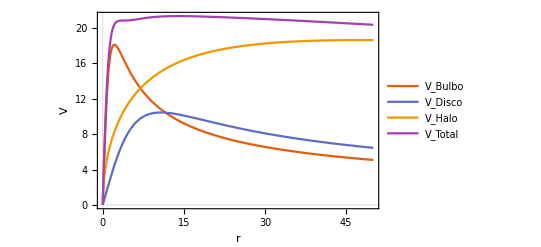

```mathematica
Plot[{VBulge[r],VDisk[r],VHalo[r],VTotal[r]},{r,0,50},PlotTheme->"Scientific",FrameLabel->{"r","V"},PlotLegends->{"V_Bulbo","V_Disco","V_Halo","V_Total"}]
```

Gráfica interactiva

```mathematica
Graphics3D[{Ellipsoid[{0,0,0},10*{1.5,1.5,1.2}],Ellipsoid[{0,0,0},10*{4,4,0.5}]}]
```

-Graphics3D-

```mathematica
CreatePoints[n_]:=Block[{pointsBulk,pointsHalo},
pointsBulk = RandomPoint[Ellipsoid[{0,0,0},10*{1.5,1.5,1.2}],n];
pointsHalo = RandomPoint[Ellipsoid[{0,0,0},10*{4,4,0.5}],Floor[n/2]];
Join[pointsBulk,pointsHalo]
];

CalculateOrbitWithoutDarkMatter[{x0_,y0_,z0_},{vx0_,vy0_,vz0_},tMax_ :100]:=Block[{x,y,z},
First@NDSolve[
{
x''[t] == axClassic[x[t],y[t],z[t]],
y''[t] == ayClassic[x[t],y[t],z[t]],
z''[t] == azClassic[x[t],y[t],z[t]],
x[0] == x0,x'[0] == vx0,y[0] == y0,y'[0]==vy0,z[0] == z0,z'[0]==vz0
},
{x,y,z},
{t,0,tMax}
]
];
CalculateOrbit[{x0_,y0_,z0_},{vx0_,vy0_,vz0_},tMax_ :100]:=Block[{x,y,z},
First@NDSolve[
{
x''[t] == ax[x[t],y[t],z[t]],
y''[t] == ay[x[t],y[t],z[t]],
z''[t] == az[x[t],y[t],z[t]],
x[0] == x0,x'[0] == vx0,y[0] == y0,y'[0]==vy0,z[0] == z0,z'[0]==vz0
},
{x,y,z},
{t,0,tMax}
]
];
CalculateInitialVelocity[{x_,y_,z_}]:={y/(√(x^2+y^2)),-x/(√(x^2+y^2)),0};
```

```mathematica
Needs["AdvancedMapping`"];
```

```mathematica
simulatedOrbit = ProgressMap[CalculateOrbitWithoutDarkMatter[#,25*CalculateInitialVelocity[#]]&,CreatePoints[10000]];
```

```mathematica
sample = RandomSample[simulatedOrbit,4000];
Manipulate[
ListPointPlot3D[
Evaluate[{x[t],y[t],z[t]}/.sample],
PlotRange->{{-60,60},{-60,60},{-60,60}},
PlotStyle->{White,PointSize[Small]},
Background->Black,
ImageSize->600
],
{t,0,10}
]
```

```mathematica
ExportName[file_,i_,total_]:=Block[{indexLength,directory,name},
indexLength = Length[IntegerDigits[total]];
directory = DirectoryName[file];
name = FileBaseName[file];
FileNameJoin[{directory,StringJoin[name,IntegerString[i,10,indexLength],".png"]}]
];
```

```mathematica
GalaxyPlot[simulatedOrbit_,t_]:=ListPointPlot3D[
Evaluate[{x[t],y[t],z[t]}/.simulatedOrbit],
PlotRange->{{-60,60},{-60,60},{-60,60}},
PlotStyle->{White,PointSize[Small]},
Background->Black,
ImageSize->600
];
```

```mathematica
ProgressTable[
Export[
ExportName[FileNameJoin[{NotebookDirectory[],"img","image.png"}],Floor[t/0.01],Floor[10/0.01]],
GalaxyPlot[simulatedOrbit,t]
],
{t,0,10,0.01}
];
```

$Aborted